```mathematica
dados3 = Import["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/Kutta_1a_3w0.dat",  "Table"]
```

{{0,0,1,0},{1,0.01,0.99995,-0.00990001},{2,0.02,0.999803,-0.0196001},{3,0.03,0.999559,-0.0291005},{4,0.04,0.999221,-0.0384016},7990,{7995,79.95,-0.0587492,-0.0538427},{7996,79.96,-0.0592611,-0.0485318},{7997,79.97,-0.0597197,-0.0431773},{7998,79.98,-0.0601245,-0.0377839},{7999,79.99,-0.0604753,-0.0323565}}
 |  |  |  |

```mathematica
xt3 = dados3[[All, {2,3}]]
```

{{0,1},{0.01,0.99995},{0.02,0.999803},{0.03,0.999559},{0.04,0.999221},{0.05,0.998792},{0.06,0.998272},{0.07,0.997664},{0.08,0.99697},7983,{79.92,-0.0568983},{79.93,-0.0575673},{79.94,-0.0581844},{79.95,-0.0587492},{79.96,-0.0592611},{79.97,-0.0597197},{79.98,-0.0601245},{79.99,-0.0604753}}
 |  |  |  |

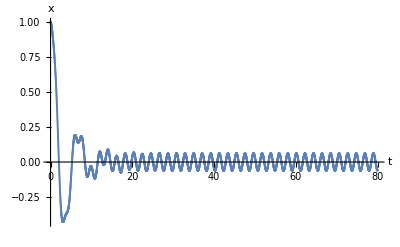

```mathematica
figxt3 = ListPlot[xt3, PlotRange->All, AxesLabel->{"t", "x"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figxt3",figxt3, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figxt3

```mathematica
vt3 = dados3[[All, {2,4}]]
```

{{0,0},{0.01,-0.00990001},{0.02,-0.0196001},{0.03,-0.0291005},{0.04,-0.0384016},{0.05,-0.047504},{0.06,-0.0564083},{0.07,-0.0651154},7984,{79.92,-0.0694657},{79.93,-0.0643143},{79.94,-0.0591051},{79.95,-0.0538427},{79.96,-0.0485318},{79.97,-0.0431773},{79.98,-0.0377839},{79.99,-0.0323565}}
 |  |  |  |

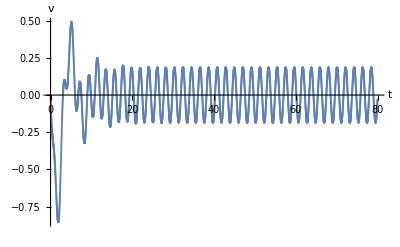

```mathematica
figvt3 = ListPlot[vt3, PlotRange->All, AxesLabel->{"t", "v"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvt3",figvt3, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvt3

```mathematica
vx3 = dados3[[All, {3,4}]]
```

{{1,0},{0.99995,-0.00990001},{0.999803,-0.0196001},{0.999559,-0.0291005},{0.999221,-0.0384016},{0.998792,-0.047504},{0.998272,-0.0564083},7987,{-0.0581844,-0.0591051},{-0.0587492,-0.0538427},{-0.0592611,-0.0485318},{-0.0597197,-0.0431773},{-0.0601245,-0.0377839},{-0.0604753,-0.0323565}}
 |  |  |  |

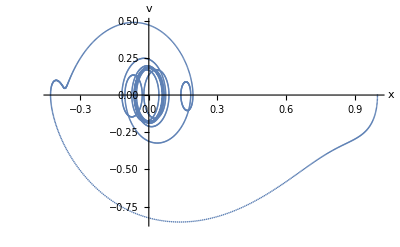

```mathematica
figvx3 =ListPlot[vx3, PlotRange->All, AxesLabel->{"x", "v"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvx3",figvx3, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvx3

```mathematica
dados2 = Import["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/Kutta_1a_w0.dat",  "Table"]
```

{{0,0,1,0},{1,0.01,0.99995,-0.00994992},{2,0.02,0.999801,-0.0197993},{3,0.03,0.999555,-0.0295478},{4,0.04,0.999211,-0.0391949},7990,{7995,79.95,0.159923,-0.987129},{7996,79.96,0.150044,-0.988679},{7997,79.97,0.14015,-0.99013},{7998,79.98,0.130242,-0.991482},{7999,79.99,0.12032,-0.992735}}
 |  |  |  |

{{0,1},{0.01,0.99995},{0.02,0.999801},{0.03,0.999555},{0.04,0.999211},{0.05,0.998771},{0.06,0.998236},{0.07,0.997608},{0.08,0.996886},7982,{79.91,0.19927},{79.92,0.189461},{79.93,0.179632},{79.94,0.169786},{79.95,0.159923},{79.96,0.150044},{79.97,0.14015},{79.98,0.130242},{79.99,0.12032}}
 |  |  |  |

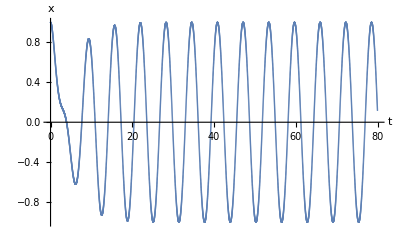

```mathematica
xt2 = dados2[[All, {2,3}]]
figxt2 = ListPlot[xt2, PlotRange->All, AxesLabel->{"t", "x"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figxt2",figxt2, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figxt2

{{0,0},{0.01,-0.00994992},{0.02,-0.0197993},{0.03,-0.0295478},{0.04,-0.0391949},{0.05,-0.04874},{0.06,-0.0581829},{0.07,-0.0675232},{0.08,-0.0767603},7983,{79.92,-0.981888},{79.93,-0.983734},{79.94,-0.985481},{79.95,-0.987129},{79.96,-0.988679},{79.97,-0.99013},{79.98,-0.991482},{79.99,-0.992735}}
 |  |  |  |

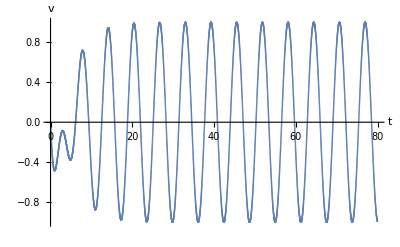

```mathematica
vt2 = dados2[[All, {2,4}]]
figvt2 = ListPlot[vt2, PlotRange->All, AxesLabel->{"t", "v"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvt2",figvt2, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvt2

```mathematica
vx2 = dados2[[All, {3,4}]]
```

{{1,0},{0.99995,-0.00994992},{0.999801,-0.0197993},{0.999555,-0.0295478},{0.999211,-0.0391949},{0.998771,-0.04874},{0.998236,-0.0581829},7986,{0.179632,-0.983734},{0.169786,-0.985481},{0.159923,-0.987129},{0.150044,-0.988679},{0.14015,-0.99013},{0.130242,-0.991482},{0.12032,-0.992735}}
 |  |  |  |

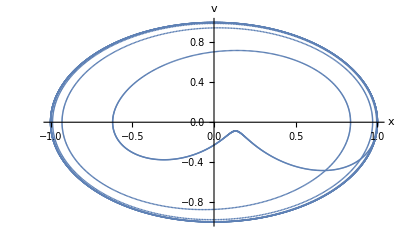

```mathematica
figvx2 =ListPlot[vx2, PlotRange->All, AxesLabel->{"x", "v"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvx2",figvx2, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvx2

```mathematica
dados1 = Import["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/Kutta_1a_w0_3.dat",  "Table"]
```

{{0,0,1,0},{1,0.01,0.99995,-0.00996656},{2,0.02,0.999801,-0.0198658},{3,0.03,0.999553,-0.029697},{4,0.04,0.999207,-0.0394597},7990,{7995,79.95,0.537165,0.0436063},{7996,79.96,0.537599,0.0430092},{7997,79.97,0.538026,0.0424117},{7998,79.98,0.538447,0.0418136},{7999,79.99,0.538862,0.0412151}}
 |  |  |  |

{{0,1},{0.01,0.99995},{0.02,0.999801},{0.03,0.999553},{0.04,0.999207},{0.05,0.998764},{0.06,0.998224},{0.07,0.997589},{0.08,0.996858},7982,{79.91,0.535374},{79.92,0.53583},{79.93,0.536281},{79.94,0.536726},{79.95,0.537165},{79.96,0.537599},{79.97,0.538026},{79.98,0.538447},{79.99,0.538862}}
 |  |  |  |

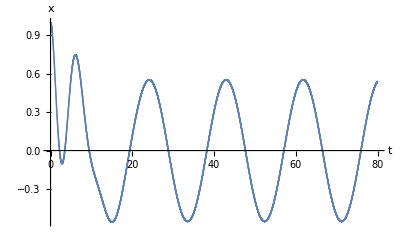

```mathematica
xt1 = dados1[[All, {2,3}]]
figxt1 = ListPlot[xt1, PlotRange->All, AxesLabel->{"t", "x"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figxt1",figxt1, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figxt1

{{0,0},{0.01,-0.00996656},{0.02,-0.0198658},{0.03,-0.029697},{0.04,-0.0394597},{0.05,-0.049153},{0.06,-0.0587766},{0.07,-0.0683296},{0.08,-0.0778115},7983,{79.92,0.0453947},{79.93,0.0447991},{79.94,0.0442029},{79.95,0.0436063},{79.96,0.0430092},{79.97,0.0424117},{79.98,0.0418136},{79.99,0.0412151}}
 |  |  |  |

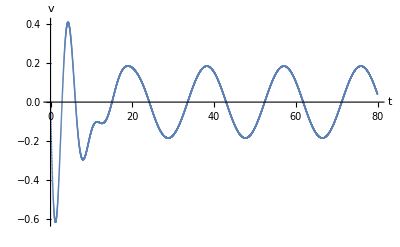

```mathematica
vt1 = dados1[[All, {2,4}]]
figvt1 = ListPlot[vt1, PlotRange->All, AxesLabel->{"t", "v"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvt1",figvt1, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvt1

```mathematica
vx1 = dados1[[All, {3,4}]]
```

{{1,0},{0.99995,-0.00996656},{0.999801,-0.0198658},{0.999553,-0.029697},{0.999207,-0.0394597},{0.998764,-0.049153},{0.998224,-0.0587766},7986,{0.536281,0.0447991},{0.536726,0.0442029},{0.537165,0.0436063},{0.537599,0.0430092},{0.538026,0.0424117},{0.538447,0.0418136},{0.538862,0.0412151}}
 |  |  |  |

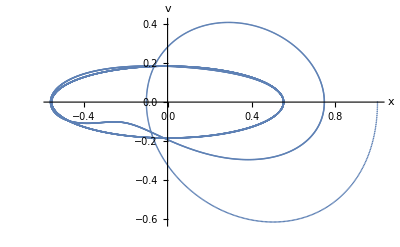

```mathematica
figvx1 =ListPlot[vx1, PlotRange->All, AxesLabel->{"x", "v"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvx1",figvx1, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/1a/figvx1